# NFourierSeries

Find a numerical approximation for an exponential Fourier series expansion of a function

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
HoldPattern[Options[NFourierSeries]] ^:= Replace[ToExpression["FourierSeries`NFourierSeries", InputForm, HoldComplete], HoldComplete[sym_] :> Options[sym]]
 
HoldPattern[SetOptions[NFourierSeries, opts___]] ^:= Replace[ToExpression["FourierSeries`NFourierSeries", InputForm, HoldComplete], HoldComplete[sym_] :> SetOptions[sym, opts]]
 
NFourierSeries[args___] := (Block[{$ContextPath}, Needs["FourierSeries`"]]; Symbol["FourierSeries`NFourierSeries"] @@ HoldComplete[args])
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

NFourierSeries[expr,t,n]

gives a numerical approximation to the n^th-order Fourier series expansion of expr in t.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The numerical approximation to the order n Fourier exponential series expansion of expr is by default defined to be ∑_(k=-n)^n F_k ⅇ^ⅈkt, where F_k is given by 1/(2π)NIntegratepaclet:ref/NIntegrate[expr ⅇ^-ⅈkt,{t,-π,π}].

With the setting FourierParameterspaclet:ref/FourierParameters->{a,b}, the order n Fourier exponential series expansion computed by NFourierSeries is (|b/(2π)|)^(1-a/2)∑_(k=-n)^n F_k ⅇ^ⅈbkt, where F_k is given by (|b/(2 π)|)^((a+1)/2)NIntegratepaclet:ref/NIntegrate[expr ⅇ^-ⅈbkt,{t,-π/(|b|),π/(|b|)}].

In addition to the option FourierParameterspaclet:ref/FourierParameters, NFourierSeries can also accept the options available to NIntegratepaclet:ref/NIntegrate. These options are passed directly to NIntegratepaclet:ref/NIntegrate.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Numerical approximation for an exponential Fourier series:

```mathematica
NFourierSeries[Sin[Cos[t]]+Abs[t]/5,t, 4,FourierParameters->{1,-2π}] //Chop
```

0.867987-0.00581111 ⅇ^(-2 ⅈ π t)-0.00581111 ⅇ^(2 ⅈ π t)-0.00382812 ⅇ^(-4 ⅈ π t)-0.00382812 ⅇ^(4 ⅈ π t)-0.000536883 ⅇ^(-6 ⅈ π t)-0.000536883 ⅇ^(6 ⅈ π t)-0.000966977 ⅇ^(-8 ⅈ π t)-0.000966977 ⅇ^(8 ⅈ π t)

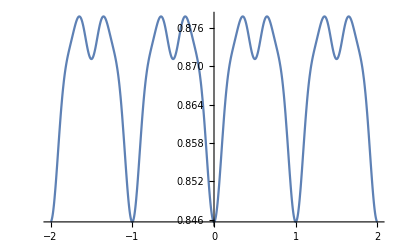

```mathematica
Plot[%, {t,-2,2}]
```

Compare with a plot of the original function:

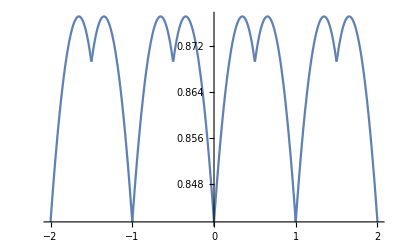

```mathematica
Plot[Sin[Cos[(t-Round[t])]]+Abs[t-Round[t]]/5, {t,-2, 2}]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Wolfram Research

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

fourier series

fourier exponential series

fourier transform

numerical approximation

inverse fourier

### Categories

Symbolic & Numeric Computation

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

FourierSeries

FourierTransform

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Tutorial: Fourier Series Package

Guide: Fourier Series Package

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.